# Music notation tests

```mathematica
Needs["MusicNotation`",FileNameJoin[{NotebookDirectory[],"MusicNotation.m"}]]
```

```mathematica
Needs["Test`",FileNameJoin[{$HomeDirectory,"mmaWorkspace","Test","Test.m"}]]
```

```mathematica
testDirectory=FileNameJoin[{NotebookDirectory[],"TestData"}]
```

/Users/eric/mmaWorkspace/MusicNotation2/TestData

## ReadScoreFile

```mathematica
VerboseOn[];
```

```mathematica
AnonymousVoiceName="~anonymous voice~";
```

```mathematica
Expected[noFile]=EmptyScore[];
Actual[noFile]=ReadScoreFile[FileNameJoin[{testDirectory,"noFile.rmn"}]];
```

ReadScoreFile::no file exists: No file exists for "/Users/eric/mmaWorkspace/MusicNotation2/TestData/noFile.rmn"

```mathematica
Expected[badExtension]=EmptyScore[];
Actual[badExtension]=ReadScoreFile[FileNameJoin[{testDirectory,"badExtension.mn"}]];
```

ReadScoreFile::bad extension: Unrecognized extension in filename "badExtension.mn"

```mathematica
Expected[justScale]=Score[ScoreInformation[],{Voice[AnonymousVoiceName,{Measure[{0,Chord[0]},{1/8,Chord[2]},{2/8,Chord[4]},{3/8,Chord[5]},{4/8,Chord[7]},{5/8,Chord[9]},{6/8,Chord[11]},{7/8,Chord[12]}]}]}];
Actual[justScale]=ReadScoreFile[FileNameJoin[{testDirectory,"justScale.rmn"}]];
```

```mathematica
Expected[badNote]=Score[ScoreInformation[],{Voice[AnonymousVoiceName,{Measure[{0,Chord[0]},{1/8,Chord[2]},{2/8,Chord[4]},{3/8,Chord[5]},{4/8,Chord[7]},{5/8,Chord[9]},{6/8,Chord[11]},{7/8,Silence[]}]}]}];
Actual[badNote]=ReadScoreFile[FileNameJoin[{testDirectory,"badNote.rmn"}]];
```

```mathematica
Expected[twoEmptyLines]=Score[ScoreInformation[],{EmptyVoice[]}];
Actual[twoEmptyLines]=ReadScoreFile[FileNameJoin[{testDirectory,"twoEmptyLines.rmn"}]];
```

```mathematica
Expected[twoEmptyMeasures1]=Score[ScoreInformation[],{Voice[AnonymousVoiceName,{Measure[],Measure[]}]}];
Actual[twoEmptyMeasures1]=ReadScoreFile[FileNameJoin[{testDirectory,"twoEmptyMeasures1.rmn"}]];
```

```mathematica
Expected[scaleWithOneInfoItem]=Score[ScoreInformation[Association["composer"->"anonymous composer"]],{Voice[AnonymousVoiceName,{Measure[{0,Chord[0]},{1/8,Chord[2]},{2/8,Chord[4]},{3/8,Chord[5]},{4/8,Chord[7]},{5/8,Chord[9]},{6/8,Chord[11]},{7/8,Chord[12]}]}]}];
Actual[scaleWithOneInfoItem]=ReadScoreFile[FileNameJoin[{testDirectory,"scaleWithOneInfoItem.rmn"}]];
```

```mathematica
Expected[scaleWithTwoInfoItems]=Score[ScoreInformation[Association["composer"->"anonymous composer","datedate"->"2015 7 14"]],{Voice[AnonymousVoiceName,{Measure[{0,Chord[0]},{1/8,Chord[2]},{2/8,Chord[4]},{3/8,Chord[5]},{4/8,Chord[7]},{5/8,Chord[9]},{6/8,Chord[11]},{7/8,Chord[12]}]}]}];
Actual[scaleWithTwoInfoItems]=ReadScoreFile[FileNameJoin[{testDirectory,"scaleWithTwoInfoItems.rmn"}]];
```

```mathematica
Expected[twoVoices]=Score[ScoreInformation[],{Voice["one",{Measure[{0,Chord[0]},{1/8,Chord[2]},{2/8,Chord[4]},{3/8,Chord[5]},{4/8,Chord[7]},{5/8,Chord[9]},{6/8,Chord[11]},{7/8,Chord[12]}]}],Voice["two",{Measure[{0,Chord[-5]},{1/8,Chord[-3]},{2/8,Chord[-1]},{3/8,Chord[0]},{4/8,Chord[2]},{5/8,Chord[4]},{6/8,Chord[6]},{7/8,Chord[7]}]}]}];
Actual[twoVoices]=ReadScoreFile[FileNameJoin[{testDirectory,"twoVoices.rmn"}]];
```

```mathematica
AssertEqual[TaggedTests]
```

{Pass_badExtension,Pass_badNote,Pass_justScale,Pass_noFile,Pass_scaleWithOneInfoItem,Pass_scaleWithTwoInfoItems,Pass_twoEmptyLines,Pass_twoEmptyMeasures1,Pass_twoVoices}

## Display

```mathematica
ReadScoreFile[FileNameJoin[{testDirectory,"noFile.rmn"}]]
```

ReadScoreFile::no file exists: No file exists for "/Users/eric/mmaWorkspace/MusicNotation2/TestData/noFile.rmn"

Score[ScoreInformation[],{Voice[,{Measure[]}]}]

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"noFile.rmn"}]]]
```

ReadScoreFile::no file exists: No file exists for "/Users/eric/mmaWorkspace/MusicNotation2/TestData/noFile.rmn"

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose[rmn`DisplayRow[0.0454545,0.5,10,Function[rmn`n,If[OddQ[rmn`n],Black,Green]]][Transpose[{}]]]

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"badExtension.rmn"}]]]
```

ReadScoreFile::no file exists: No file exists for "/Users/eric/mmaWorkspace/MusicNotation2/TestData/badExtension.rmn"

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose[rmn`DisplayRow[0.0454545,0.5,10,Function[rmn`n,If[OddQ[rmn`n],Black,Green]]][Transpose[{}]]]

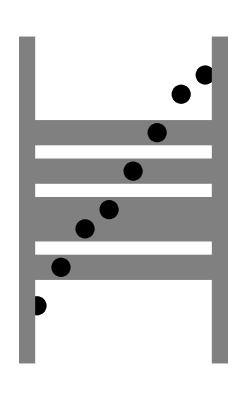

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"justScale.rmn"}]]]
```

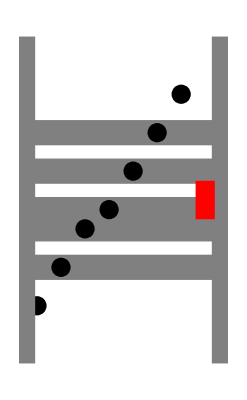

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"badNote.rmn"}]]]
```

```mathematica
ReadScoreFile[FileNameJoin[{testDirectory,"twoEmptyLines.rmn"}]]
```

Score[ScoreInformation[],{Voice[,{Measure[]}]}]

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"twoEmptyLines.rmn"}]]]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose[rmn`DisplayRow[0.0454545,0.5,10,Function[rmn`n,If[OddQ[rmn`n],Black,Green]]][Transpose[{}]]]

```mathematica
ReadScoreFile[FileNameJoin[{testDirectory,"twoEmptyMeasures1.rmn"}]]
```

Score[ScoreInformation[],{Voice[~anonymous voice~,{Measure[],Measure[]}]}]

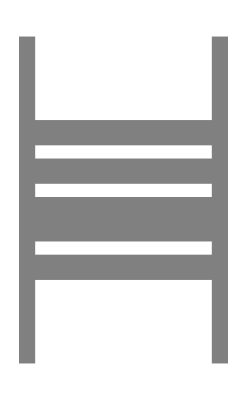
{{-Graphics-,-Graphics-}}

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"twoEmptyMeasures1.rmn"}]]]
```

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"scaleWithOneInfoItem.rmn"}]]]
```

{{-Graphics-}}

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"scaleWithTwoInfoItems.rmn"}]]]
```

{{-Graphics-}}

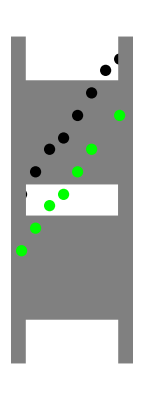

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"twoVoices.rmn"}]]]
```

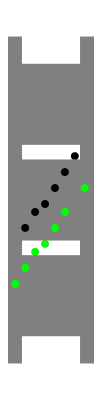
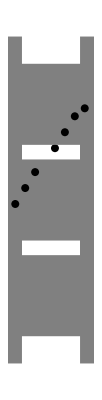

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"twoUnevenVoices.rmn"}]]]
```

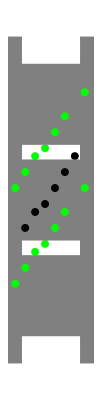
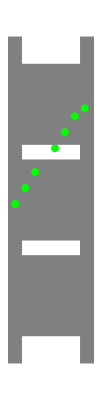

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"twoVoicesWithChords.rmn"}]]]
```

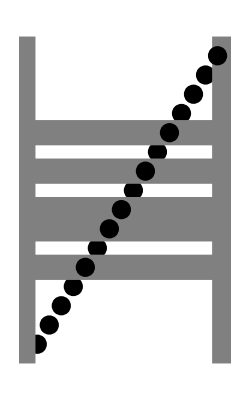

```mathematica
DisplayScore[ReadScoreFile[FileNameJoin[{testDirectory,"maxRangeForOneStaff.rmn"}]]]
```